## Lab08

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

## Problem 1

```mathematica
(* Problem 1 Rotate an equilateral triangle RT=2 at the distance RR=7/2 from the origin. Rotate the triangle around itself.
The code highlighted by Cyan is attached to the Lab manual. 
*)
```

```mathematica
RT=2;
```

```mathematica
(* Shift the triangle along x *)
```

```mathematica
RR={7/2,0};
```

```mathematica
(* Center *)
```

```mathematica
CTri={0,0};
```

```mathematica
(* Shift the x coordinate by RR *)
```

```mathematica
Tri=RegularPolygon[CTri,RT,3]
```

```mathematica
(* Indicate the center by a point  *)
```

```mathematica
CTriP={Red,Point[CTri]}
```

```mathematica
(* The Triangle and the center point *)
```

```mathematica
ObjectTri={Tri,CTriP}
```

```mathematica
(* ATTN: Compose the rotation function and apply to both the object and the centerpoint CTri. The composed transformation is generated by Composition  *)
```

```mathematica
TTri[a_]:=GeometricTransformation[ObjectTri,Composition[RotationTransform[a],TranslationTransform[RR]]]
```

```mathematica
(* Define the graphics function  *)
```

```mathematica
FTri[a_]:=Graphics[TTri[a],Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
Coord={{1,2},{2,3},{2,7},{3,8},{4,9},{5,11},{10,10},{7,8},{4,4},{2,1},{1,2}};
```

```mathematica
(* Points *)
```

```mathematica
P1={Red,PointSize->0.03,Point[Coord]}
```

```mathematica
{FTri[0], FTri[Pi/2], FTri[Pi]}
```

```mathematica
FTriC[a_]:= Graphics[{Circle[CTri, RR[[1]]] , TTri[a]}, Axes->True, AxesOrigin->{0,0}, PlotRange->5.5]
```

```mathematica
{FTriC[0], FTriC[Pi/2], FTriC[Pi]}
```

```mathematica
Manipulate[FTriC[t], {t,0,2Pi, 0.1}]
```

```mathematica
TTriPlus[a_] := GeometricTransformation[ObjectTri,Composition[RotationTransform[a],TranslationTransform[RR], RotationTransform[a]]]
```

```mathematica
FTriCPlus[a_]:= Graphics[{Circle[CTri, RR[[1]]] , TTriPlus[a]}, Axes->True, AxesOrigin->{0,0}, PlotRange->5.5]
```

```mathematica
Manipulate[FTriCPlus[t], {t,0,2Pi, 0.1}]
```

## Problem 2

6 circular point positioned equal angular distance and rotate around center

```mathematica
Graphics[{Red, Point[CirclePoints[2.5 (*radius*), 25 (*number of points*)]]}, ImageSize->Tiny, Axes->True]
```

```mathematica
pointsObject = {Red, PointSize[0.07],Point[CirclePoints[2 (*radius*), 6(*number of points*)]]};
```

```mathematica
TTriPoints[a_]:= GeometricTransformation[pointsObject, Composition[RotationTransform[a],TranslationTransform[RR]]]
```

```mathematica
FPointsCir[t_]:=Graphics[{ TTri[t],TTriPoints[t]}, Axes->True, AxesOrigin->{0,0}, PlotRange->7]
```

```mathematica
Manipulate[FPointsCir[t], {t,0,2Pi,0.1}]
```

## Problem 3

add a circle around the triangle and rotate the entire system around itself

```mathematica
circleAroundTri := {Black,Circle[{0,0}, 2]}
```

```mathematica
purpleCircleT := {Purple,Thickness[0.01],Circle[CTri, RR[[1]]]}
```

```mathematica
circleAroundTriT [a_] := GeometricTransformation[{circleAroundTri,ObjectTri}, Composition[RotationTransform[a],TranslationTransform[RR], RotationTransform[a]]]
```

```mathematica
TTriPoints[a_]:= GeometricTransformation[pointsObject, Composition[RotationTransform[a],TranslationTransform[RR], RotationTransform[a]]]
```

```mathematica
allObject[t_] :={purpleCircleT,circleAroundTriT[t],TTriPlus[t],TTriPoints[t]}
```

```mathematica
FPointsCir[t_]:=Graphics[allObject[t], Axes->True, AxesOrigin->{0,0}, PlotRange->7]
```

```mathematica
Manipulate[FPointsCir[t], {t,0,2Pi,0.1}]
```

## Problem 4 Move an rotating parametric curve

```mathematica
curveF[t_]:= {4Cos[2t], 4Sin[4t]}
```

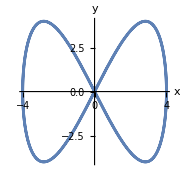

```mathematica
curveP = ParametricPlot[curveF[t], {t, 0,2Pi}]
```

```mathematica
curveG = curveP[[1]];
```

```mathematica
Graphics[curveG]
```

-Graphics-

```mathematica
TrajF[t_]:= {t,0.05t^2}
```

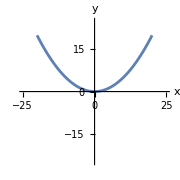

```mathematica
TrajP = ParametricPlot[TrajF[t], {t, -20,20}, PlotRange->25]
```

### Matrix rotate around origin by a and move along the trajF[t_]

#### Translation

```mathematica
Tran = TranslationTransform[TrajF[t]]
```

TransformationFunction[(1. | 0. | 1.5
0. | 1. | 0.1125
0. | 0. | 1.)]

```mathematica
MTran = TransformationMatrix[Tran]
```

{{1.,0.,1.5},{0.,1.,0.1125},{0.,0.,1.}}

```mathematica
FTran[t_] := Evaluate[MTran]
```

```mathematica
MatrixForm[FTran[t]]
```

(1. | 0. | 1.5
0. | 1. | 0.1125
0. | 0. | 1.)

#### Rotation

```mathematica
Rot = RotationTransform[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

```mathematica
MRot = TransformationMatrix[Rot]
```

{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}

```mathematica
FRot[t_] := Evaluate[MRot]
```

```mathematica
MatrixForm[FRot[t]]
```

(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)

### combine 2 transformation - matrix multiplication

```mathematica
MAll[a_,t_] = FTran[t].FRot[a]
```

{{0.+1. Cos[a],0.-1. Sin[a],1.5},{0.+1. Sin[a],0.+1. Cos[a],0.1125},{0.,0.,1.}}

```mathematica
MatrixForm[MAll[a,t]]
```

(0.+1. Cos[a] | 0.-1. Sin[a] | 1.5
0.+1. Sin[a] | 0.+1. Cos[a] | 0.1125
0. | 0. | 1.)

### H-Coordinate of curve object

```mathematica
ObH[s_]:= {4Cos[2s], 4Sin[4s],1}
```

```mathematica
Res[a_,t_,s_]:= (MAll[a,t].ObH[s])[[1;;2]]
```

```mathematica
MatrixForm[Res[a,t,s]]
```

(1.5+4 (0.+1. Cos[a]) Cos[2 s]+4 (0.-1. Sin[a]) Sin[4 s]
0.1125+4 Cos[2 s] (0.+1. Sin[a])+4 (0.+1. Cos[a]) Sin[4 s])

```mathematica
pres[a_,t_] :=ParametricPlot[Res[a,t,s], {s,-0,2Pi}, PlotRange->6, PlotStyle->Red]
```

```mathematica
Manipulate[Show[TrajP,pres[8a,t]], {a,0,2Pi}, {t,-20,20}]
```

```mathematica
T[a_]:= -20 + (20a/Pi)
```

```mathematica
Manipulate[{Show[TrajP, pres[a,T[a]]], "a=", a, "T[a]=", T[a]}, {a,0,2Pi}]
```

### use rotation matrix to rotate the entire system

#### Rotation Matrix for ObH[s]

```mathematica
ObH[t_]:= {4Cos[2t], 4Sin[4t],1}
```

```mathematica
MNew [a_,t_]= FRot[a].FTran[t].FRot[a]
```

{{Cos[a] (0.+1. Cos[a])+(0.-1. Sin[a]) Sin[a],Cos[a] (0.-1. Sin[a])-(0.+1. Cos[a]) Sin[a],0.+1.5 Cos[a]-0.1125 Sin[a]},{(0.+1. Cos[a]) Sin[a]+Cos[a] (0.+1. Sin[a]),Cos[a] (0.+1. Cos[a])-Sin[a] (0.+1. Sin[a]),0.+0.1125 Cos[a]+1.5 Sin[a]},{0.,0.,1.}}

```mathematica
ResNew[a_,t_,s_] = (MNew[a,t].ObH[s])[[1;;2]]
```

{0.+1.5 Cos[a]-0.1125 Sin[a]+4 Cos[2 s] (Cos[a] (0.+1. Cos[a])+(0.-1. Sin[a]) Sin[a])+4 (Cos[a] (0.-1. Sin[a])-(0.+1. Cos[a]) Sin[a]) Sin[4 s],0.+0.1125 Cos[a]+1.5 Sin[a]+4 Cos[2 s] ((0.+1. Cos[a]) Sin[a]+Cos[a] (0.+1. Sin[a]))+4 (Cos[a] (0.+1. Cos[a])-Sin[a] (0.+1. Sin[a])) Sin[4 s]}

```mathematica
presNew[a_,t_]:= ParametricPlot[ResNew[a,t,s], {s,-0,2Pi} ,PlotRange->6, PlotStyle->Red]
```

#### Rotate Matrix for the trajectory H-Coordinate

```mathematica
TrajH[s_] := {s,0.05s^2,1}
```

```mathematica
TrajNew[a_,s_]= (FRot[a].TrajH[s])[[1;;2]]
```

{s Cos[a]-0.05 s^2 Sin[a],0.05 s^2 Cos[a]+s Sin[a]}

```mathematica
MatrixForm[TrajNew[a,s]]
```

(s Cos[a]-0.05 s^2 Sin[a]
0.05 s^2 Cos[a]+s Sin[a])

```mathematica
presTraj[a_] := ParametricPlot[TrajNew[a,s], {s,-20,20}, PlotRange->25]
```

```mathematica
Manipulate[Show[presTraj[a], presNew[a,T[a]]], {a,0,2Pi}]
```